```mathematica
Quit
```

```mathematica
(* Cosmo Theory *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
(* Vanilla wCDM *)
dLwCDM[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
HwCDM[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
(* Growth for wCDM models *)
δwCDM[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δwCDM[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δwCDM[a,w,Ω]/δwCDM[1,w,Ω]
ΣwCDM[a_,w_,Ω_]:=2
ηwCDM[a_,w_,Ω_]:=1
EgwCDM[a_,w_,Ω_]:=(Ω ΣwCDM[a,w,Ω])/(2fwCDM[a,w,Ω])
P2wCDM[a_,w_,Ω_]:=2 EgwCDM[a,w,Ω]
P3wCDM[a_,w_,Ω_,σ8_]:=a D[Log[fσ8wCDM[aa,w,Ω,σ8]],aa]/.aa->a
```

```mathematica
(* Various params *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
Neff=3.044;
KtoeV=8.621738*10^-5;
```

```mathematica
(* DE equation of state w(a) and energy density f(a) *)
w[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
ρde[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
```

```mathematica
(* H(z) and χ^2 for the nCPL model *) 
ρcr[h_]:=8.098*10^-11 h^2 eV^4;
Ωγ[h_]:=Pi^2/30 gγ T^4/ρcr[h]/.T->Tcmb K/.gγ->2/.GeV->10^9 eV/.K->KtoeV eV;
Ων[h_,Neff_]:=Neff*7/8(4/11)^(4/3)Ωγ[h]
aeq[om_,h_]:=(Ωγ[h]+Ων[h,Neff])/om;
H[a_,om_,w0_,wa_,n_,h_]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))ρde[a,w0,wa,n]]
(* The Geff and lensing potential. Not that in this notation: Geff=1 and Σ=2 in GR! *)
Geff[a_,ga_,m1_]:=1+ga (1-a)^m1-ga (1-a)^(2m1)
Σ[a_,σa_,m2_]:=2+σa (1-a)^m2-σa (1-a)^(2m2)
```

```mathematica
(* Solve the ODE for the growth *)
Clear[solgr,δ,fσ8,Eg]
aini=10^-4;
solgr[om_,w0_,wa_,n_,h_,ga_,m1_]:=solgr[om,w0,wa,n,h,ga,m1]=NDSolve[{δ''[a]+(3/a+(D[H[aa,om,w0,wa,n,h],aa]/.aa->a)/H[a,om,w0,wa,n,h])δ'[a]-3/2(om Geff[a,ga,m1])/(a^5(H[a,om,w0,wa,n,h]/H[1,om,w0,wa,n,h])^2)δ[a]==0,δ[aini]==aini,δ'[aini]==1},δ,{a,aini,1},Method->Automatic]
(* Define the growth-rate, fσ8 and Eg *)
f[a_,om_,w0_,wa_,n_,h_,ga_,m1_]:=a δ'[a]/δ[a]/.solgr[om,w0,wa,n,h,ga,m1][[1]]
fσ8[a_,om_,w0_,wa_,n_,h_,ga_,m1_,σ8_]:=σ8/δ[1] a δ'[a]/.solgr[om,w0,wa,n,h,ga,m1][[1]]
Eg[a_,om_,w0_,wa_,n_,h_,ga_,m1_,σ8_,σa_,m2_]:=(om Σ[a,σa,m2])/(2f[a,om,w0,wa,n,h,ga,m1])/.solgr[om,w0,wa,n,h,ga,m1][[1]]
```

```mathematica
(* The fiducial cosmology for LCDM and a test *)
a0=1/(1+0.1);
om0=0.3;
w00=-1;
wa0=0;
n0=1;
h0=0.7;
ga0=-0.627;
σa0=-3.562;
m10=2;
m20=2;
σ80=0.8;
{fσ8[a0,om0,w00,wa0,n0,h0,ga0,m10,σ80],Eg[a0,om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20],f[a0,om0,w00,wa0,n0,h0,ga0,m10]}
{fσ8wCDM[a0,w00,om0,σ80],EgwCDM[a0,w00,om0],fwCDM[a0,w00,om0]}
```

{0.4127,0.54555,0.541877}

{0.433864,0.525324,0.571076}

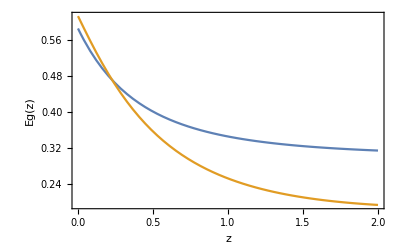

```mathematica
Plot[{EgwCDM[1/(1+z),w00,om0],Eg[1/(1+z),om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20]},{z,0,2},Frame->True,FrameLabel->{"z","Eg(z)"},FrameStyle->Black]
```

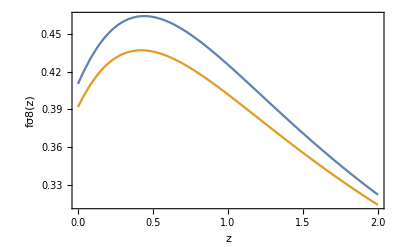

```mathematica
Plot[{fσ8wCDM[1/(1+z),w00,om0,σ80],fσ8[1/(1+z),om0,w00,wa0,n0,h0,ga0,m10,σ80]},{z,0,2},Frame->True,FrameLabel->{"z","fσ8(z)"},FrameStyle->Black]
```

```mathematica
{fσ8[a0,om0,w00,wa0,n0,h0,0,m10,σ80],
fσ8[a0,om0,w00,wa0,n0,h0,ga0,m10,σ80]}
{Eg[a0,om0,w00,wa0,n0,h0,0,m10,0,σa0,m20],Eg[a0,om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20]}
```

{0.433838,0.4127}

{0.517687,0.54555}

```mathematica
(* Assume 20 bins in [0,2] *)
zeff=MovingAverage[Subdivide [0,2,20],2]//N
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95}

```mathematica
(* The mocks *)
SeedRandom[154];
mockH=Table[{zeff[[i]],RandomVariate[NormalDistribution[H[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0],0.01*H[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0]]],0.01*H[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0]},{i,1,Length[zeff]}];
mockfσ8=Table[{zeff[[i]],RandomVariate[NormalDistribution[fσ8[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0,ga0,m10,σ80],0.01*fσ8[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0,ga0,m10,σ80]]],0.01*fσ8[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0,ga0,m10,σ80]},{i,1,Length[zeff]}];
mockEg=Table[{zeff[[i]],RandomVariate[NormalDistribution[Eg[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20],0.01*Eg[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20]]],0.01*Eg[1/(1+zeff[[i]]),om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20]},{i,1,Length[zeff]}];

(* The χ^2 *)
chi2H[om_,w0_,wa_,n_,h_]:=Sum[(((mockH[[i,2]]-H[1/(1+mockH[[i,1]]),om,w0,wa,n,h])/mockH[[i,3]]))^2,{i,1,Length[mockH]}];
chi2fσ8[om_?NumericQ,w0_?NumericQ,wa_?NumericQ,n_?NumericQ,h_?NumericQ,ga_?NumericQ,m1_?NumericQ,σ8_?NumericQ]:=Sum[((1/mockfσ8[[i,3]](mockfσ8[[i,2]]-fσ8[1/(1+mockfσ8[[i,1]]),om,w0,wa,n,h,ga,m1,σ8])))^2,{i,1,Length[mockfσ8]}];
chi2Eg[om_?NumericQ,w0_?NumericQ,wa_?NumericQ,n_?NumericQ,h_?NumericQ,ga_?NumericQ,m1_?NumericQ,σ8_?NumericQ,σa_?NumericQ,m2_?NumericQ]:=Sum[((1/mockEg[[i,3]](mockEg[[i,2]]-Eg[1/(1+mockEg[[i,1]]),om,w0,wa,n,h,ga,m1,σ8,σa,m2])))^2,{i,1,Length[mockEg]}];
```

```mathematica
chi2H[om0,w00,wa0,n0,h0]
chi2fσ8[om0,w00,wa0,n0,h0,ga0,m10,σ80]
chi2Eg[om0,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20]
```

19.8083

20.3204

19.5932

```mathematica
(* Best fits *)
FindMinimum[chi2H[om,w00,wa0,n0,h0],{om,0.3,0.31}]
FindMinimum[chi2fσ8[om,w00,wa0,n0,h0,ga0,m10,σ80],{om,0.3,0.31}]
FindMinimum[chi2Eg[om,w00,wa0,n0,h0,ga0,m10,σ80,σa0,m20],{om,0.3,0.31}]
```

{17.8418,{om→0.297102}}

{17.029,{om→0.294425}}

{16.9532,{om→0.301384}}

```mathematica
Export["mock_H_Geff.txt",mockH,"Table"]
Export["mock_fs8_Geff.txt",mockfσ8,"Table"]
Export["mock_Eg_Geff.txt",mockEg,"Table"]
```

mock_H_Geff.txt

mock_fs8_Geff.txt

mock_Eg_Geff.txt

```mathematica
(* end *)
```